```mathematica
Nt = 551 ;(*151*)
ti = 0; tf =1; 
deltat = (tf - ti) /Nt ;
Nx = 551; (*151*)
(*xi = -2; xf = 8; *)
(*xi = 0; xf = 2*Pi;*)
xi = 0; xf = 2*Pi;
deltax = (xf - xi) / Nx;
c = 1;
r = c * (deltat / deltax)//N
k = .;
j  = .;
```

0.159155

```mathematica
(************************************************************************************************************************)
(*Set Up*)
(************************************************************************************************************************)
h = N[(2*Pi)/ (Nx),32];

T = N[Table[tn = ti + n *deltat, {n, 0, Nt -1 }],32];
Xo = N[Table[xn = xi + n *deltax, {n, 0, Nx -1}],32];

X = N[(Xo-xi)*((2*Pi))/(xf-xi),32];

f[x_] = ⅇ^(- 8(x-π)^2);
```

```mathematica
(************************************************************************************************************************)
(*Differentiation Matrix*)
(************************************************************************************************************************)
```

```mathematica
D1 = N[Table[If[ k≠ j, 1/2(-1)^(k - j)Csc[((k - j) * h)/2],0],{k,1,Nx},{j,1,Nx}],32];
D2 = N[MatrixPower[D1,2],32];
DL = N[-c * D1 * deltat,32];
```

```mathematica
(*CN*)
UCN= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
UCN[[1,All]] = N[f[X],32];
UCN = N[UCN,32];
UCN = Chop[UCN, 10^(-307)];
UCN = Developer`ToPackedArray[UCN, Real]; 
Developer`PackedArrayQ[UCN]

UCNold= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
UCNold[[1,All]] = N[f[X],32];
UCNold = N[UCNold,32];
UCNold = Chop[UCNold, 10^(-307)];
UCNold = Developer`ToPackedArray[UCNold, Real]; 
Developer`PackedArrayQ[UCNold]


I1 = N[IdentityMatrix[Length[D1]],32];
A = N[I1 - ((DL / 2)),32];
B = N[I1 + ((DL / 2)),32];
MCN = N[Inverse[A].B,32];
EMCN = N[MCN - I1,32];
EMCN = Developer`ToPackedArray[EMCN, Real]; 

Do[UCNold[[n+1,All]] = UCNold[[n,All]] + (EMCN).UCNold[[n,All]], {n,1,Nt - 1 }];

yerr = 0;
Do[
Do[
delta = (EMCN[[m,All]]).UCN[[n,All]] + yerr;
UCN[[n+1,m]] = UCN[[n,m]] +  delta;
yerr = (UCN[[n,m]] - UCN[[n+1,m]]) + delta

,{m,1,Length[EMCN]}]
,{n,1,Nt - 1}]
```

True

True

```mathematica
(************************************************************************************************************************)
```

```mathematica
(*Energy*)
```

```mathematica
(************************************************************************************************************************)
```

```mathematica
(*CN*)
FCN = Table[0,{i,1,Nt},{j,1,Nx}];
FCN = Developer`ToPackedArray[FCN, Real];
intCN = Table[0,{i,1,Length[FCN[[All,1]]]}];
intCN = Developer`ToPackedArray[intCN, Real];

FCNold = Table[0,{i,1,Nt},{j,1,Nx}];
FCNold = Developer`ToPackedArray[FCNold, Real];
intCNold = Table[0,{i,1,Length[FCNold[[All,1]]]}];
intCNold = Developer`ToPackedArray[intCNold, Real];
Do[
FCN[[i]] = (D1.UCN[[i,All]])^2;

intCN[[i]] = (2π)/Nx Total[FCN[[i,All]]]
,{i,1,Length[FCN[[All,1]]]}];

Do[
FCNold[[i]] = (D1.UCNold[[i,All]])^2;

intCNold[[i]] = (2π)/Nx Total[FCNold[[i,All]]]
,{i,1,Length[FCNold[[All,1]]]}];
```

```mathematica
energyErrorLD2 = Abs[intCN - intCN[[1]]];
energyErrorLD2old = Abs[intCNold - intCNold[[1]]];
energyErrorLD2 - energyErrorLD2old
```

{0.,3.10862×10^-15,5.77316×10^-15,-3.9968×10^-15,1.11022×10^-14,2.22045×10^-15,2.66454×10^-15,-1.77636×10^-15,2.22045×10^-15,-5.77316×10^-15,-9.76996×10^-15,5.32907×10^-15,-1.42109×10^-14,-1.77636×10^-15,2.22045×10^-15,7.54952×10^-15,-1.77636×10^-15,-1.55431×10^-14,0.,9.32587×10^-15,8.88178×10^-16,4.44089×10^-16,-1.02141×10^-14,-1.33227×10^-15,-5.77316×10^-15,-5.77316×10^-15,-7.10543×10^-15,1.59872×10^-14,5.77316×10^-15,-8.88178×10^-16,4.44089×10^-15,-1.24345×10^-14,4.44089×10^-16,-1.06581×10^-14,5.32907×10^-15,7.54952×10^-15,2.22045×10^-15,3.9968×10^-15,-7.54952×10^-15,7.54952×10^-15,5.32907×10^-15,-8.43769×10^-15,-2.22045×10^-15,-3.9968×10^-15,6.66134×10^-15,3.10862×10^-15,-1.28786×10^-14,4.88498×10^-15,1.33227×10^-15,-3.10862×10^-15,-4.88498×10^-15,-6.66134×10^-15,-3.9968×10^-15,-5.32907×10^-15,4.44089×10^-16,-4.88498×10^-15,-3.55271×10^-15,0.,6.66134×10^-15,4.88498×10^-15,-1.73195×10^-14,6.66134×10^-15,-4.44089×10^-15,-1.77636×10^-15,3.9968×10^-15,9.32587×10^-15,9.76996×10^-15,1.15463×10^-14,-1.33227×10^-15,8.43769×10^-15,-4.44089×10^-16,4.44089×10^-15,1.11022×10^-14,2.66454×10^-15,3.10862×10^-15,3.55271×10^-15,1.77636×10^-15,1.11022×10^-14,1.06581×10^-14,-1.19904×10^-14,9.32587×10^-15,4.88498×10^-15,7.54952×10^-15,1.11022×10^-14,3.9968×10^-15,8.88178×10^-16,-8.88178×10^-16,-1.33227×10^-15,-1.42109×10^-14,-3.55271×10^-15,8.88178×10^-16,-2.66454×10^-15,3.9968×10^-15,1.59872×10^-14,4.44089×10^-16,7.99361×10^-15,0.,2.66454×10^-15,-2.66454×10^-15,1.24345×10^-14,-1.06581×10^-14,-1.33227×10^-15,3.10862×10^-15,4.44089×10^-16,0.,8.88178×10^-16,7.99361×10^-15,2.66454×10^-15,-7.10543×10^-15,5.77316×10^-15,6.66134×10^-15,-9.32587×10^-15,0.,1.73195×10^-14,8.88178×10^-15,1.06581×10^-14,2.66454×10^-15,-8.88178×10^-16,-7.99361×10^-15,2.66454×10^-15,-1.77636×10^-15,-1.24345×10^-14,1.33227×10^-15,7.54952×10^-15,8.88178×10^-16,1.77636×10^-15,-1.06581×10^-14,5.77316×10^-15,1.64313×10^-14,7.10543×10^-15,1.15463×10^-14,1.46549×10^-14,4.88498×10^-15,1.24345×10^-14,1.24345×10^-14,-1.33227×10^-15,8.88178×10^-15,9.32587×10^-15,-3.9968×10^-15,7.54952×10^-15,9.32587×10^-15,-4.88498×10^-15,-4.44089×10^-15,6.21725×10^-15,-8.88178×10^-16,1.33227×10^-15,-3.9968×10^-15,-1.02141×10^-14,8.88178×10^-16,1.73195×10^-14,3.55271×10^-15,2.66454×10^-15,1.33227×10^-14,7.54952×10^-15,1.59872×10^-14,6.21725×10^-15,-1.5099×10^-14,7.10543×10^-15,-7.99361×10^-15,-1.59872×10^-14,-9.32587×10^-15,2.44249×10^-14,2.66454×10^-15,1.82077×10^-14,-3.10862×10^-15,4.88498×10^-15,-4.44089×10^-16,2.53131×10^-14,-3.10862×10^-15,9.76996×10^-15,-4.44089×10^-15,-4.44089×10^-15,4.88498×10^-15,1.46549×10^-14,-2.66454×10^-15,3.55271×10^-15,-2.66454×10^-15,2.66454×10^-15,2.66454×10^-15,-1.33227×10^-15,1.24345×10^-14,-1.59872×10^-14,1.37668×10^-14,1.95399×10^-14,-9.32587×10^-15,-1.15463×10^-14,8.43769×10^-15,-6.21725×10^-15,1.77636×10^-15,-1.33227×10^-15,4.88498×10^-15,-1.33227×10^-15,1.37668×10^-14,9.76996×10^-15,2.66454×10^-15,9.76996×10^-15,1.28786×10^-14,-2.66454×10^-15,0.,2.66454×10^-15,-8.88178×10^-16,-9.32587×10^-15,6.66134×10^-15,0.,1.24345×10^-14,-1.33227×10^-15,1.19904×10^-14,7.54952×10^-15,-3.55271×10^-15,2.22045×10^-15,6.21725×10^-15,3.55271×10^-15,1.15463×10^-14,1.33227×10^-14,-1.77636×10^-15,-6.21725×10^-15,6.21725×10^-15,1.19904×10^-14,-1.19904×10^-14,7.99361×10^-15,3.55271×10^-15,7.99361×10^-15,1.82077×10^-14,1.06581×10^-14,0.,3.10862×10^-15,-1.77636×10^-15,-3.10862×10^-15,2.66454×10^-15,2.22045×10^-15,1.15463×10^-14,-3.10862×10^-15,8.88178×10^-16,-4.88498×10^-15,1.5099×10^-14,2.66454×10^-15,1.06581×10^-14,-5.77316×10^-15,1.82077×10^-14,7.99361×10^-15,1.28786×10^-14,2.66454×10^-15,2.22045×10^-15,-1.33227×10^-15,-2.66454×10^-15,-9.76996×10^-15,1.02141×10^-14,2.39808×10^-14,2.66454×10^-15,0.,-1.77636×10^-15,-8.88178×10^-15,4.88498×10^-15,1.33227×10^-15,2.66454×10^-15,1.06581×10^-14,1.37668×10^-14,1.06581×10^-14,8.43769×10^-15,7.10543×10^-15,1.33227×10^-15,-2.22045×10^-15,5.77316×10^-15,2.22045×10^-15,1.77636×10^-14,-4.88498×10^-15,7.99361×10^-15,8.88178×10^-15,-1.19904×10^-14,-7.10543×10^-15,4.88498×10^-15,7.10543×10^-15,1.28786×10^-14,8.88178×10^-16,5.77316×10^-15,1.82077×10^-14,3.9968×10^-15,9.76996×10^-15,0.,2.22045×10^-15,-8.88178×10^-15,1.55431×10^-14,4.44089×10^-15,1.15463×10^-14,1.82077×10^-14,8.88178×10^-15,-1.37668×10^-14,2.04281×10^-14,-4.88498×10^-15,8.88178×10^-15,1.06581×10^-14,1.06581×10^-14,-2.22045×10^-15,1.33227×10^-14,1.46549×10^-14,-1.95399×10^-14,7.54952×10^-15,1.19904×10^-14,6.21725×10^-15,2.22045×10^-15,3.55271×10^-15,6.21725×10^-15,1.55431×10^-14,-6.21725×10^-15,1.28786×10^-14,1.68754×10^-14,1.77636×10^-15,1.19904×10^-14,7.10543×10^-15,5.32907×10^-15,1.5099×10^-14,2.66454×10^-15,3.9968×10^-15,2.08722×10^-14,3.9968×10^-15,-2.22045×10^-15,1.77636×10^-14,4.88498×10^-15,1.55431×10^-14,-4.44089×10^-16,6.66134×10^-15,1.86517×10^-14,-3.9968×10^-15,1.68754×10^-14,-2.66454×10^-15,-8.43769×10^-15,1.77636×10^-14,2.08722×10^-14,2.66454×10^-15,-2.66454×10^-15,0.,-4.44089×10^-15,3.9968×10^-15,-1.59872×10^-14,5.32907×10^-15,1.42109×10^-14,1.33227×10^-14,-7.99361×10^-15,6.21725×10^-15,1.24345×10^-14,7.10543×10^-15,5.32907×10^-15,1.24345×10^-14,-1.06581×10^-14,3.10862×10^-15,7.54952×10^-15,3.9968×10^-15,3.15303×10^-14,-7.99361×10^-15,-8.88178×10^-16,-1.64313×10^-14,1.59872×10^-14,4.88498×10^-15,1.15463×10^-14,8.88178×10^-15,1.28786×10^-14,-7.54952×10^-15,8.43769×10^-15,1.24345×10^-14,-4.88498×10^-15,3.9968×10^-15,8.43769×10^-15,8.88178×10^-16,1.28786×10^-14,6.21725×10^-15,-7.54952×10^-15,1.46549×10^-14,1.33227×10^-15,-3.9968×10^-15,0.,3.28626×10^-14,1.24345×10^-14,1.19904×10^-14,1.19904×10^-14,2.22045×10^-15,-5.77316×10^-15,3.41949×10^-14,6.21725×10^-15,4.88498×10^-15,-5.32907×10^-15,3.55271×10^-15,-7.99361×10^-15,7.10543×10^-15,4.26326×10^-14,1.33227×10^-14,2.30926×10^-14,0.,3.9968×10^-15,6.21725×10^-15,1.15463×10^-14,4.44089×10^-15,2.22045×10^-14,1.42109×10^-14,-2.22045×10^-15,7.99361×10^-15,6.21725×10^-15,1.68754×10^-14,1.55431×10^-14,4.44089×10^-15,4.88498×10^-15,6.21725×10^-15,1.73195×10^-14,6.66134×10^-15,3.15303×10^-14,-1.77636×10^-15,-3.10862×10^-15,1.19904×10^-14,3.9968×10^-15,-3.55271×10^-15,-5.77316×10^-15,5.32907×10^-15,-7.10543×10^-15,1.42109×10^-14,1.11022×10^-14,7.10543×10^-15,-4.88498×10^-15,7.99361×10^-15,1.37668×10^-14,1.11022×10^-14,-3.55271×10^-15,1.68754×10^-14,7.54952×10^-15,2.04281×10^-14,6.21725×10^-15,5.77316×10^-15,-2.22045×10^-15,4.44089×10^-15,3.06422×10^-14,1.55431×10^-14,-7.10543×10^-15,0.,-3.9968×10^-15,1.33227×10^-14,2.17604×10^-14,1.82077×10^-14,4.88498×10^-15,4.44089×10^-16,1.68754×10^-14,1.06581×10^-14,2.13163×10^-14,9.76996×10^-15,-7.10543×10^-15,-8.43769×10^-15,1.59872×10^-14,-2.66454×10^-15,1.15463×10^-14,2.22045×10^-15,2.22045×10^-15,-1.33227×10^-14,4.88498×10^-15,8.43769×10^-15,-1.33227×10^-14,-2.22045×10^-15,2.35367×10^-14,3.10862×10^-15,5.77316×10^-15,-3.55271×10^-15,7.10543×10^-15,5.32907×10^-15,1.06581×10^-14,1.33227×10^-15,2.13163×10^-14,2.30926×10^-14,-5.77316×10^-15,2.4869×10^-14,-7.54952×10^-15,1.5099×10^-14,-8.88178×10^-16,2.22045×10^-14,1.02141×10^-14,1.19904×10^-14,1.33227×10^-14,-4.44089×10^-16,1.64313×10^-14,0.,9.32587×10^-15,1.59872×10^-14,-4.44089×10^-16,1.33227×10^-14,2.39808×10^-14,1.46549×10^-14,1.55431×10^-14,1.02141×10^-14,1.02141×10^-14,1.82077×10^-14,4.88498×10^-15,-1.82077×10^-14,1.55431×10^-14,2.4869×10^-14,1.90958×10^-14,7.10543×10^-15,1.06581×10^-14,8.43769×10^-15,1.11022×10^-14,1.33227×10^-15,1.59872×10^-14,2.44249×10^-14,1.46549×10^-14,1.19904×10^-14,1.82077×10^-14,1.37668×10^-14,0.,2.22045×10^-14,1.19904×10^-14,2.26485×10^-14,7.54952×10^-15,1.37668×10^-14,2.04281×10^-14,1.68754×10^-14,-3.10862×10^-15,-4.88498×10^-15,1.11022×10^-14,4.26326×10^-14,2.79776×10^-14,3.10862×10^-15,5.77316×10^-15,1.9984×10^-14,1.90958×10^-14,1.46549×10^-14,1.15463×10^-14,1.77636×10^-15,1.86517×10^-14,2.70894×10^-14,9.32587×10^-15,-4.44089×10^-16,2.17604×10^-14,1.06581×10^-14,1.06581×10^-14,1.86517×10^-14,1.77636×10^-15,2.35367×10^-14,5.77316×10^-15,3.9968×10^-14,0.,5.77316×10^-15,6.21725×10^-15,2.66454×10^-15,3.9968×10^-15,3.10862×10^-15,2.30926×10^-14,1.9984×10^-14,2.22045×10^-15,1.95399×10^-14,2.44249×10^-14,8.43769×10^-15,1.64313×10^-14,1.24345×10^-14,6.21725×10^-15,1.46549×10^-14,9.76996×10^-15,1.11022×10^-14}

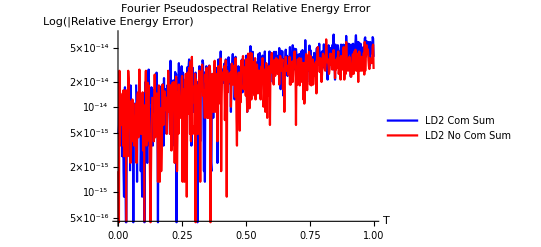

```mathematica
ListLogPlot[{Transpose[{T,energyErrorLD2}],Transpose[{T,energyErrorLD2old}]},PlotStyle->{Blue,Red},PlotLegends->{"LD2 Com Sum", "LD2 No Com Sum"},AxesLabel->{"T","Log(|Relative Energy Error)"},PlotLabel->"Fourier Pseudospectral Relative Energy Error",PlotRange->{{ti,tf},{0,Max[energyErrorLD2]}},Joined->True]
```

```mathematica
(*exportData=Flatten/@Transpose[{T,energyErrorLD2, energyErrorLD4, energyErrorRK2, energyErrorRK4}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\Energy_Error_Pseudospectral.dat",exportData,"Table"];*)
```

```mathematica
(*exportDataRK4Stable=Flatten/@Transpose[{T,intRK4}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\FDM_RK4_Stable_Energy.dat",exportDataRK4Stable,"Table"];*)
```

```mathematica
(************************************************************************************************************************)
(*L1 Error*)
(************************************************************************************************************************)
```

```mathematica
fexact[t_,x_] = ⅇ^(- 8((x-t)-π)^2);
Uexact = Table[fexact[T[[i]],X[[j]]],{i,1,Nt},{j,1,Nx}];
Uexact = Chop[N[Uexact], 10^(-307)];
Uexact = Developer`ToPackedArray[Uexact, Real];
```

```mathematica
(*LD2*)
abserrLD2 = Abs[UCN-Uexact];
errorLD2 = Table[0,{i,1,Length[abserrLD2]}];
errorLD2 = Developer`ToPackedArray[errorLD2, Real];
Do[
errorLD2[[i]] = Norm[abserrLD2[[i,All]], 1] * deltax;
,{i,1,Length[errorLD2]}
];
(*ListLinePlot[Transpose[{T,errorLD2}],PlotRange->All]*)

abserrLD2old = Abs[UCNold-Uexact];
errorLD2old = Table[0,{i,1,Length[abserrLD2old]}];
errorLD2old = Developer`ToPackedArray[errorLD2old, Real];
Do[
errorLD2old[[i]] = Norm[abserrLD2old[[i,All]], 1] * deltax;
,{i,1,Length[errorLD2old]}
];

errorLD2 - errorLD2old
```

{0.,-9.82743×10^-18,6.96102×10^-19,-3.30707×10^-18,-5.09075×10^-18,1.42662×10^-18,-1.18697×10^-17,-1.29313×10^-17,1.7973×10^-19,1.27574×10^-18,-1.57277×10^-17,-1.36922×10^-17,-1.83864×10^-17,-2.18263×10^-17,-2.43451×10^-17,-3.09768×10^-17,-3.97302×10^-17,-4.49205×10^-17,-5.36426×10^-17,-5.25065×10^-17,-5.50999×10^-17,-3.85814×10^-17,-3.28408×10^-17,-5.14072×10^-17,-4.61928×10^-17,-3.65467×10^-17,-3.08908×10^-17,-2.05951×10^-17,-1.6201×10^-17,-3.02002×10^-17,-1.74939×10^-17,-1.75199×10^-17,-1.09142×10^-17,-8.5779×10^-18,8.19081×10^-19,-1.28618×10^-17,-5.43181×10^-18,7.14599×10^-18,-1.45986×10^-18,-1.26138×10^-17,-1.35402×10^-17,-2.78229×10^-17,-4.43924×10^-17,-4.15097×10^-17,-3.29794×10^-17,-2.34099×10^-17,-2.8448×10^-17,-5.74627×10^-18,-5.12103×10^-17,-5.21397×10^-17,-5.81899×10^-17,-5.93406×10^-17,-6.17474×10^-17,-5.05382×10^-17,-5.98909×10^-17,-6.70225×10^-17,-5.56869×10^-17,-4.91758×10^-17,-3.65639×10^-17,-3.03704×10^-17,-4.89934×10^-17,-3.74965×10^-17,-3.14359×10^-17,-3.74753×10^-17,-4.21204×10^-17,-4.23398×10^-17,-4.52565×10^-17,-6.31179×10^-17,-5.18122×10^-17,-5.41453×10^-17,-4.42825×10^-17,-4.72572×10^-17,-3.06677×10^-17,-5.4042×10^-17,-5.44028×10^-17,-5.27104×10^-17,-3.78848×10^-17,-3.74431×10^-17,-4.18756×10^-17,-5.26922×10^-17,-5.20557×10^-17,-4.15804×10^-17,-4.81356×10^-17,-4.19379×10^-17,-2.99278×10^-17,-5.00584×10^-17,-4.10053×10^-17,-3.50744×10^-17,-3.36641×10^-17,-2.84501×10^-17,-2.52153×10^-17,-7.09348×10^-18,-2.68535×10^-17,-2.01276×10^-17,-2.38745×10^-17,-1.70491×10^-17,-1.01394×10^-17,-1.38575×10^-18,-1.41497×10^-17,-7.1083×10^-18,-1.5474×10^-17,-1.07565×10^-17,-1.20685×10^-17,-1.19737×10^-17,-1.91743×10^-17,-1.95008×10^-17,-1.62817×10^-17,-2.24265×10^-17,-1.49442×10^-17,3.53636×10^-18,1.73718×10^-17,-2.42675×10^-18,-4.42659×10^-18,-1.53025×10^-17,-2.62953×10^-17,-3.10912×10^-17,-2.87559×10^-17,-5.50021×10^-17,-4.60439×10^-17,-4.51871×10^-17,-4.26566×10^-17,-4.34541×10^-17,-3.95603×10^-17,-5.42868×10^-17,-5.35473×10^-17,-5.28011×10^-17,-5.86558×10^-17,-4.55602×10^-17,-4.82385×10^-17,-6.57459×10^-17,-5.80251×10^-17,-4.17096×10^-17,-4.29937×10^-17,-5.26736×10^-17,-6.27389×10^-17,-4.43972×10^-17,-7.72935×10^-17,-7.59738×10^-17,-7.51979×10^-17,-7.79694×10^-17,-6.90103×10^-17,-6.62575×10^-17,-7.72824×10^-17,-8.38317×10^-17,-7.25043×10^-17,-6.22967×10^-17,-4.82758×10^-17,-6.36494×10^-17,-6.04638×10^-17,-6.02867×10^-17,-7.42475×10^-17,-7.95483×10^-17,-7.58493×10^-17,-7.34987×10^-17,-3.36382×10^-17,-7.84225×10^-17,-9.2103×10^-17,-1.0002×10^-16,-1.11797×10^-16,-1.13657×10^-16,-1.18995×10^-16,-1.01929×10^-16,-1.00842×10^-16,-1.13721×10^-16,-1.31842×10^-16,-1.38652×10^-16,-1.56866×10^-16,-1.42319×10^-16,-1.50635×10^-16,-1.61935×10^-16,-1.67238×10^-16,-1.79075×10^-16,-1.84621×10^-16,-1.59679×10^-16,-1.59893×10^-16,-1.58399×10^-16,-1.60742×10^-16,-1.52847×10^-16,-1.70651×10^-16,-1.64857×10^-16,-1.75775×10^-16,-1.83148×10^-16,-1.82308×10^-16,-1.85629×10^-16,-1.89172×10^-16,-2.06527×10^-16,-1.93172×10^-16,-1.99532×10^-16,-1.99395×10^-16,-1.95924×10^-16,-1.95012×10^-16,-2.09014×10^-16,-2.07809×10^-16,-2.15536×10^-16,-2.19986×10^-16,-2.23539×10^-16,-2.18494×10^-16,-2.1879×10^-16,-1.73748×10^-16,-2.18385×10^-16,-2.28363×10^-16,-2.30591×10^-16,-2.32793×10^-16,-2.29676×10^-16,-2.50718×10^-16,-2.3041×10^-16,-2.43021×10^-16,-2.39547×10^-16,-2.40282×10^-16,-2.33535×10^-16,-2.3874×10^-16,-2.15721×10^-16,-2.33089×10^-16,-2.43809×10^-16,-2.45048×10^-16,-2.32772×10^-16,-2.32356×10^-16,-2.06621×10^-16,-2.18529×10^-16,-2.16883×10^-16,-2.30247×10^-16,-2.37779×10^-16,-2.37383×10^-16,-2.16292×10^-16,-2.55681×10^-16,-2.7078×10^-16,-2.73869×10^-16,-2.72582×10^-16,-2.69053×10^-16,-2.74413×10^-16,-2.57075×10^-16,-2.61597×10^-16,-2.76003×10^-16,-2.84895×10^-16,-2.883×10^-16,-2.77422×10^-16,-2.39676×10^-16,-2.55079×10^-16,-2.49988×10^-16,-2.76595×10^-16,-2.74692×10^-16,-2.75103×10^-16,-1.90397×10^-16,-2.46481×10^-16,-2.54873×10^-16,-2.47029×10^-16,-2.61643×10^-16,-2.54419×10^-16,-2.61488×10^-16,-2.30051×10^-16,-2.59269×10^-16,-2.79546×10^-16,-2.90482×10^-16,-3.02484×10^-16,-2.97735×10^-16,-2.48877×10^-16,-2.83033×10^-16,-2.87402×10^-16,-3.05174×10^-16,-3.10155×10^-16,-3.15264×10^-16,-2.72562×10^-16,-2.90393×10^-16,-3.01483×10^-16,-3.21884×10^-16,-3.30536×10^-16,-3.26353×10^-16,-2.93063×10^-16,-2.8155×10^-16,-3.10632×10^-16,-3.37866×10^-16,-3.53394×10^-16,-3.50892×10^-16,-3.35007×10^-16,-2.74127×10^-16,-3.02918×10^-16,-3.26055×10^-16,-3.37292×10^-16,-3.47378×10^-16,-3.33153×10^-16,-2.90473×10^-16,-2.82782×10^-16,-2.97476×10^-16,-3.14098×10^-16,-3.3543×10^-16,-3.31427×10^-16,-2.3485×10^-16,-2.74376×10^-16,-3.0036×10^-16,-3.12326×10^-16,-3.28898×10^-16,-3.30658×10^-16,-3.21032×10^-16,-2.53639×10^-16,-2.52057×10^-16,-2.62104×10^-16,-2.92921×10^-16,-3.14363×10^-16,-3.12769×10^-16,-2.59926×10^-16,-2.58823×10^-16,-2.92428×10^-16,-3.19858×10^-16,-3.55164×10^-16,-3.64248×10^-16,-3.07871×10^-16,-2.96363×10^-16,-3.07451×10^-16,-3.27309×10^-16,-3.61868×10^-16,-3.71531×10^-16,-3.3442×10^-16,-2.94603×10^-16,-2.87923×10^-16,-3.11688×10^-16,-3.37605×10^-16,-3.65083×10^-16,-3.77606×10^-16,-3.16484×10^-16,-3.00399×10^-16,-3.12745×10^-16,-3.46829×10^-16,-3.76782×10^-16,-4.04424×10^-16,-3.50545×10^-16,-3.40284×10^-16,-3.26819×10^-16,-3.54161×10^-16,-3.74765×10^-16,-4.02156×10^-16,-3.1284×10^-16,-3.50231×10^-16,-3.39428×10^-16,-3.49921×10^-16,-3.65×10^-16,-3.85214×10^-16,-3.70702×10^-16,-3.28422×10^-16,-3.25484×10^-16,-3.27033×10^-16,-3.40999×10^-16,-3.71539×10^-16,-3.99449×10^-16,-3.58124×10^-16,-3.5353×10^-16,-3.47167×10^-16,-3.3903×10^-16,-3.45452×10^-16,-3.757×10^-16,-3.37758×10^-16,-3.41678×10^-16,-3.49557×10^-16,-3.51054×10^-16,-3.64958×10^-16,-3.92618×10^-16,-3.98687×10^-16,-3.8087×10^-16,-3.82159×10^-16,-3.71299×10^-16,-3.72881×10^-16,-3.85969×10^-16,-4.11106×10^-16,-3.69161×10^-16,-3.79002×10^-16,-3.79901×10^-16,-3.86821×10^-16,-3.98351×10^-16,-4.19723×10^-16,-3.82422×10^-16,-4.1188×10^-16,-4.24358×10^-16,-4.15056×10^-16,-4.21152×10^-16,-4.3124×10^-16,-3.69008×10^-16,-4.24965×10^-16,-4.39275×10^-16,-4.36673×10^-16,-4.22551×10^-16,-4.26386×10^-16,-4.18853×10^-16,-3.99845×10^-16,-4.3159×10^-16,-4.40516×10^-16,-4.19879×10^-16,-4.13305×10^-16,-4.20752×10^-16,-3.68297×10^-16,-4.08858×10^-16,-4.23037×10^-16,-4.08073×10^-16,-3.82039×10^-16,-3.77548×10^-16,-3.26191×10^-16,-3.74294×10^-16,-4.04065×10^-16,-4.04653×10^-16,-3.84182×10^-16,-3.69169×10^-16,-2.66045×10^-16,-3.33982×10^-16,-3.91638×10^-16,-4.09408×10^-16,-3.91078×10^-16,-3.67955×10^-16,-3.6767×10^-16,-3.19614×10^-16,-3.78029×10^-16,-4.22429×10^-16,-4.20681×10^-16,-4.03472×10^-16,-3.83094×10^-16,-3.00436×10^-16,-3.58998×10^-16,-4.2396×10^-16,-4.53151×10^-16,-4.35968×10^-16,-4.11582×10^-16,-2.73844×10^-16,-3.45806×10^-16,-4.24746×10^-16,-4.74804×10^-16,-4.87176×10^-16,-4.47545×10^-16,-3.9023×10^-16,-3.36809×10^-16,-3.97431×10^-16,-4.69587×10^-16,-5.01523×10^-16,-4.70723×10^-16,-4.186×10^-16,-3.08357×10^-16,-3.49567×10^-16,-4.35161×10^-16,-4.94925×10^-16,-4.99548×10^-16,-4.59944×10^-16,-3.23279×10^-16,-3.38053×10^-16,-4.08134×10^-16,-4.86858×10^-16,-5.15726×10^-16,-4.96011×10^-16,-3.27536×10^-16,-3.37499×10^-16,-3.79806×10^-16,-4.61069×10^-16,-5.21318×10^-16,-5.08355×10^-16,-4.66456×10^-16,-3.3159×10^-16,-3.54934×10^-16,-4.4168×10^-16,-5.02612×10^-16,-5.27458×10^-16,-4.911×10^-16,-3.42025×10^-16,-3.53884×10^-16,-4.22537×10^-16,-5.03358×10^-16,-5.5143×10^-16,-5.36932×10^-16,-3.58178×10^-16,-3.41834×10^-16,-3.76274×10^-16,-4.63115×10^-16,-5.47385×10^-16,-5.70956×10^-16,-5.06802×10^-16,-3.60944×10^-16,-3.73247×10^-16,-4.5651×10^-16,-5.51529×10^-16,-5.96355×10^-16,-5.5923×10^-16,-3.70906×10^-16,-3.65396×10^-16,-4.25432×10^-16,-5.31593×10^-16,-6.1149×10^-16,-6.2552×10^-16,-4.59029×10^-16,-4.2569×10^-16,-4.47401×10^-16,-5.28337×10^-16,-6.15375×10^-16,-6.59012×10^-16,-5.11738×10^-16,-4.90286×10^-16,-4.70164×10^-16,-5.17242×10^-16,-5.93291×10^-16,-6.63811×10^-16,-6.67723×10^-16,-4.96507×10^-16,-4.75785×10^-16,-4.96748×10^-16,-5.63433×10^-16,-6.39007×10^-16,-6.72143×10^-16,-5.12968×10^-16,-4.76737×10^-16,-4.73186×10^-16,-5.32023×10^-16,-6.22202×10^-16,-6.83891×10^-16,-5.49719×10^-16,-5.1649×10^-16,-4.81111×10^-16,-5.18449×10^-16,-6.07658×10^-16,-6.90474×10^-16,-7.09207×10^-16,-5.53401×10^-16,-5.09423×10^-16,-5.12265×10^-16,-5.91476×10^-16,-6.99077×10^-16,-7.50891×10^-16,-6.09162×10^-16,-5.53129×10^-16,-5.3502×10^-16,-5.78144×10^-16,-6.7125×10^-16,-7.4955×10^-16,-6.50298×10^-16,-6.19669×10^-16,-5.6762×10^-16,-5.7172×10^-16,-6.46977×10^-16,-7.4275×10^-16,-6.51101×10^-16,-6.49312×10^-16,-5.92828×10^-16,-5.608×10^-16,-6.05889×10^-16,-7.04013×10^-16,-7.80124×10^-16,-6.67066×10^-16,-6.32713×10^-16,-5.80241×10^-16,-5.88048×10^-16,-6.55038×10^-16,-7.3868×10^-16,-6.68871×10^-16,-6.50359×10^-16,-5.91944×10^-16,-5.79923×10^-16,-6.2883×10^-16,-7.2466×10^-16,-6.73439×10^-16}

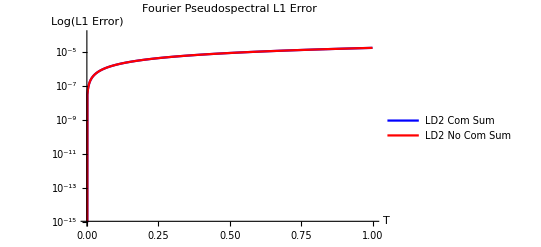

```mathematica
ListLogPlot[{Transpose[{T,errorLD2}],Transpose[{T,errorLD2old}]},PlotRange->{{ti,tf},{1*10^-15,1*10^-4}}, PlotStyle->{Blue, Red},PlotLegends->{"LD2 Com Sum", "LD2 No Com Sum"},Axes -> True, AxesLabel->{"T","Log(L1 Error)" },PlotLabel->"Fourier Pseudospectral L1 Error", Joined->True]
```